```mathematica
G0=(σoff Exp[(ρoff(z-1))/e])/(σoff+σon)Hypergeometric1F1[σon/e,1+(σon+σoff)/e,((z-1)(ρon-ρoff))/e];
G1=(σon Exp[(ρoff(z-1))/e])/(σoff+σon)Hypergeometric1F1[(e+σon)/e,1+(σon+σoff)/e,((z-1)(ρon-ρoff))/e];
G=Exp[ρoff(z-1)/e]Hypergeometric1F1[σon/e,(σon+σoff)/e,((z-1)(ρon-ρoff))/e];
```

```mathematica
pars={ρoff->1/3,ρon->30,σoff->1/2,σon->1/2,e->1};
```

```mathematica
nmax=40;
```

```mathematica
sc0=Table[SeriesCoefficient[G0/.pars,{z,0,n}],{n,0,nmax}];
sc1=Table[SeriesCoefficient[G1/.pars,{z,0,n}],{n,0,nmax}];
ser0=Table[{n,sc0[[n]]},{n,0,nmax}];
ser1=Table[{n,sc1[[n]]},{n,0,nmax}];
ser=Table[{n,sc0[[n]]+sc1[[n]]},{n,0,nmax}];
```

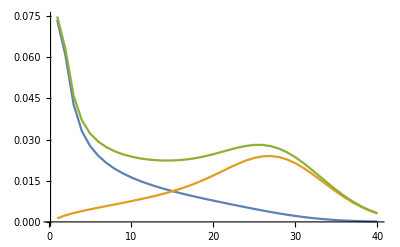

```mathematica
ListPlot[{ser0,ser1,ser},PlotRange->All,Joined->True]
```

```mathematica
Total[ser0]//N
```

{820.,1536.+List}

```mathematica
SetPrecision[ser0,100]//N
```

{{0.,List},{1.,0.0735871},{2.,0.0606802},{3.,0.0427611},{4.,0.0331051},{5.,0.027671},{6.,0.0240847},{7.,0.0214471},{8.,0.0193778},{9.,0.0176835},{10.,0.0162525},{11.,0.0150146},{12.,0.0139228},{13.,0.0129439},{14.,0.0120538},{15.,0.0112339},{16.,0.0104697},{17.,0.00974931},{18.,0.00906302},{19.,0.00840264},{20.,0.00776149},{21.,0.00713445},{22.,0.00651812},{23.,0.00591096},{24.,0.00531348},{25.,0.00472816},{26.,0.0041593},{27.,0.00361253},{28.,0.00309425},{29.,0.00261089},{30.,0.00216821},{31.,0.00177069},{32.,0.00142105},{33.,0.00112012},{34.,0.000866769},{35.,0.000658234},{36.,0.000490436},{37.,0.000358456},{38.,0.000256977},{39.,0.000180692},{40.,0.000124616}}

```mathematica
Export["./p0fig3.csv",SetPrecision[ser0,100]//N,"CSV"]
```

./p0fig3.csv